```mathematica
Table[y[i]=#[[i]],{i,4}]&@(Table[A[i,j],{i,4},{j,4}].Table[x[i],{i,4}]);
```

```mathematica
Vx=Table[x[i],{i,4}];
```

```mathematica
Vy=Table[y[i],{i,4}];
```

```mathematica
Aij=Table[A[i,j],{i,4},{j,4}];
```

```mathematica
gij={{-c^2,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
cons=Table[Aij[[i,All]].{1,b,b,0}==0,{i,2,4,1}]
```

{A[2,1]+b A[2,2]+b A[2,3]==0,A[3,1]+b A[3,2]+b A[3,3]==0,A[4,1]+b A[4,2]+b A[4,3]==0}

```mathematica
cons={A[1,1]+A[1,2]b+ A[1,3]b+ A[1,4]b==0,A[1,4]==0}
```

{A[1,1]+b A[1,2]+b A[1,3]+b A[1,4]==0}

```mathematica
Reduce[Join@@{Join@@Table[Coefficient[Expand@(Vy.gij.Vy),x[i]x[j]]==gij[[i,j]],{i,4},{j,4}],cons},Flatten@Aij[[All]]]
```

```mathematica
Reduce[Join@@{Join@@Table[Coefficient[Expand@(Vy.gij.Vy),x[i]x[j]]==gij[[i,j]],{i,4},{j,4}]/.{A[t_,4]/;t<4->0,A[4,t_]/;t<4->0,A[4,4]->1},cons},Flatten@Aij[[1;;3,1;;3]]]
```

(A[4,1]==0&&c==0&&b==0&&A[2,1]==0&&(A[2,2]==-1||A[2,2]==1)&&A[2,3]==0&&A[3,1]==0&&A[3,2]==0&&(A[3,3]==-1||A[3,3]==1)&&A[4,2]+A[4,3]≠0)||(A[4,1]==0&&c==0&&b==0&&A[2,1]==0&&(A[2,3]==-√(1-A[2,2]^2)||A[2,3]==√(1-A[2,2]^2))&&A[3,1]==0&&(A[3,2]==-√(1-A[2,2]^2)||A[3,2]==√(1-A[2,2]^2))&&-1+A[2,2]^2≠0&&A[3,3]==(A[2,2] A[2,3] A[3,2])/(-1+A[2,2]^2)&&A[4,2]+A[4,3]≠0)||(A[4,2]==-A[4,3]&&A[4,1]==0&&c==0&&b==0&&A[2,1]==0&&(A[2,2]==-1||A[2,2]==1)&&A[2,3]==0&&A[3,1]==0&&A[3,2]==0&&(A[3,3]==-1||A[3,3]==1))||(A[4,2]==-A[4,3]&&A[4,1]==0&&c==0&&b==0&&A[2,1]==0&&(A[2,3]==-√(1-A[2,2]^2)||A[2,3]==√(1-A[2,2]^2))&&A[3,1]==0&&(A[3,2]==-√(1-A[2,2]^2)||A[3,2]==√(1-A[2,2]^2))&&-1+A[2,2]^2≠0&&A[3,3]==(A[2,2] A[2,3] A[3,2])/(-1+A[2,2]^2))||(A[4,1]==0&&b==0&&(A[1,1]==-1||A[1,1]==1)&&A[1,2]==0&&A[1,3]==0&&A[2,1]==0&&(A[2,2]==-1||A[2,2]==1)&&A[2,3]==0&&A[3,1]==0&&A[3,2]==0&&(A[3,3]==-1||A[3,3]==1)&&c A[4,2]+c A[4,3]≠0)||(A[4,1]==0&&b==0&&(A[1,1]==-1||A[1,1]==1)&&A[1,2]==0&&A[1,3]==0&&A[2,1]==0&&(A[2,3]==-√(1-A[2,2]^2)||A[2,3]==√(1-A[2,2]^2))&&A[3,1]==0&&(A[3,2]==-√(1-A[2,2]^2)||A[3,2]==√(1-A[2,2]^2))&&-1+A[2,2]^2≠0&&A[3,3]==(A[2,2] A[2,3] A[3,2])/(-1+A[2,2]^2)&&c A[4,2]+c A[4,3]≠0)||(A[4,2]==-A[4,3]&&A[4,1]==0&&b==0&&(A[1,1]==-1||A[1,1]==1)&&A[1,2]==0&&A[1,3]==0&&A[2,1]==0&&(A[2,2]==-1||A[2,2]==1)&&A[2,3]==0&&A[3,1]==0&&A[3,2]==0&&(A[3,3]==-1||A[3,3]==1)&&c≠0)||(A[4,2]==-A[4,3]&&A[4,1]==0&&b==0&&(A[1,1]==-1||A[1,1]==1)&&A[1,2]==0&&A[1,3]==0&&A[2,1]==0&&(A[2,3]==-√(1-A[2,2]^2)||A[2,3]==√(1-A[2,2]^2))&&A[3,1]==0&&(A[3,2]==-√(1-A[2,2]^2)||A[3,2]==√(1-A[2,2]^2))&&-1+A[2,2]^2≠0&&A[3,3]==(A[2,2] A[2,3] A[3,2])/(-1+A[2,2]^2)&&c≠0)||(A[4,2]==-A[4,3]&&A[4,1]==0&&2 b^2-c^2≠0&&(A[1,1]==-c/(√(-2 b^2+c^2))||A[1,1]==c/(√(-2 b^2+c^2)))&&c≠0&&A[1,2]==-(b A[1,1])/c^2&&A[1,3]==A[1,2]&&(A[2,1]==-c √(-1+A[1,1]^2)||A[2,1]==c √(-1+A[1,1]^2))&&b≠0&&A[2,2]==-A[2,1]/(2 b)&&A[2,3]==A[1,1] A[1,2] A[2,1]+2 A[2,2]-2 A[2,2]^3&&A[3,1]==0&&(A[3,2]==-(√(1+A[1,1]^2-2 A[2,2]^2))/(√2)||A[3,2]==(√(1+A[1,1]^2-2 A[2,2]^2))/(√2))&&A[3,3]==(-1+A[1,1]^2-2 A[2,2]^2) A[3,2])||(A[4,2]==-A[4,3]&&A[4,1]==0&&2 b^2-c^2≠0&&(A[1,1]==-c/(√(-2 b^2+c^2))||A[1,1]==c/(√(-2 b^2+c^2)))&&c≠0&&A[1,2]==-(b A[1,1])/c^2&&A[1,3]==A[1,2]&&b≠0&&(A[2,2]==1/(2 b^2)(-b A[2,1]-√(2 b^4-2 b^2 A[2,1]^2+b^2 A[1,1]^2 A[2,1]^2-4 b^4 A[1,2]^2 A[2,1]^2))||A[2,2]==1/(2 b^2)(-b A[2,1]+√(2 b^4-2 b^2 A[2,1]^2+b^2 A[1,1]^2 A[2,1]^2-4 b^4 A[1,2]^2 A[2,1]^2)))&&A[2,3]==(-A[2,1]-b A[2,2])/b&&(A[3,1]==-√(-c^2+c^2 A[1,1]^2-A[2,1]^2)||A[3,1]==√(-c^2+c^2 A[1,1]^2-A[2,1]^2))&&-c^2+c^2 A[1,1]^2-A[2,1]^2≠0&&A[3,2]==(-b A[1,1]^2 A[3,1]-A[2,1] A[2,2] A[3,1])/(-c^2+c^2 A[1,1]^2-A[2,1]^2)&&A[3,3]==(-A[3,1]-b A[3,2])/b)||(A[4,2]+A[4,3]≠0&&b==-A[4,1]/(A[4,2]+A[4,3])&&2 b^2-c^2≠0&&(A[1,1]==-c/(√(-2 b^2+c^2))||A[1,1]==c/(√(-2 b^2+c^2)))&&c≠0&&A[1,2]==-(b A[1,1])/c^2&&A[1,3]==A[1,2]&&(A[2,1]==-c √(-1+A[1,1]^2)||A[2,1]==c √(-1+A[1,1]^2))&&b≠0&&A[2,2]==-A[2,1]/(2 b)&&A[2,3]==A[1,1] A[1,2] A[2,1]+2 A[2,2]-2 A[2,2]^3&&A[3,1]==0&&(A[3,2]==-(√(1+A[1,1]^2-2 A[2,2]^2))/(√2)||A[3,2]==(√(1+A[1,1]^2-2 A[2,2]^2))/(√2))&&A[3,3]==(-1+A[1,1]^2-2 A[2,2]^2) A[3,2])||(A[4,2]+A[4,3]≠0&&b==-A[4,1]/(A[4,2]+A[4,3])&&2 b^2-c^2≠0&&(A[1,1]==-c/(√(-2 b^2+c^2))||A[1,1]==c/(√(-2 b^2+c^2)))&&c≠0&&A[1,2]==-(b A[1,1])/c^2&&A[1,3]==A[1,2]&&b≠0&&(A[2,2]==1/(2 b^2)(-b A[2,1]-√(2 b^4-2 b^2 A[2,1]^2+b^2 A[1,1]^2 A[2,1]^2-4 b^4 A[1,2]^2 A[2,1]^2))||A[2,2]==1/(2 b^2)(-b A[2,1]+√(2 b^4-2 b^2 A[2,1]^2+b^2 A[1,1]^2 A[2,1]^2-4 b^4 A[1,2]^2 A[2,1]^2)))&&A[2,3]==(-A[2,1]-b A[2,2])/b&&(A[3,1]==-√(-c^2+c^2 A[1,1]^2-A[2,1]^2)||A[3,1]==√(-c^2+c^2 A[1,1]^2-A[2,1]^2))&&-c^2+c^2 A[1,1]^2-A[2,1]^2≠0&&A[3,2]==(-b A[1,1]^2 A[3,1]-A[2,1] A[2,2] A[3,1])/(-c^2+c^2 A[1,1]^2-A[2,1]^2)&&A[3,3]==(-A[3,1]-b A[3,2])/b)

```mathematica
Flatten@Aij[[1;;3,1;;3]]
```

{A[1,1],A[1,2],A[1,3],A[2,1],A[2,2],A[2,3],A[3,1],A[3,2],A[3,3]}

```mathematica
Grid@(Table[k[i,j],{i,2},{j,2}].{{1,1},{-1,1}})
```

k[1,1]-k[1,2] | k[1,1]+k[1,2]
k[2,1]-k[2,2] | k[2,1]+k[2,2]

```mathematica
{{1,1},{-1,1}}.{x,y}
```

{x+y,-x+y}

```mathematica
Tij={{γ,-√2 γ*β,0,0},{-√2 γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}}
```

{{γ,-√2 β γ,0,0},{-√2 β γ,γ,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Rij={{1,0,0,0},{0,1/√2,-1/√2,0},{0,1/√2,1/√2,0},{0,0,0,1}}
```

{{1,0,0,0},{0,1/(√2),-1/(√2),0},{0,1/(√2),1/(√2),0},{0,0,0,1}}

```mathematica
{{1,0,0,0},{0,1/(√2),-1/(√2),0},{0,1/(√2),1/(√2),0},{0,0,0,1}}
```

```mathematica
Rij.Tij.(Inverse@Rij)
```

{{γ,-β γ,-β γ,0},{-β γ,1/2+γ/2,-1/2+γ/2,0},{-β γ,-1/2+γ/2,1/2+γ/2,0},{0,0,0,1}}

```mathematica
γ[t_]:=1/(√(1-β[t]^2))
DSolve[-c*γ[t]*γ'[t]+γ[t]*β[t]*D[γ[t]*β[t]*c,t]==0,β[t],t]
```

{{}}

```mathematica
D[1/(√(1-β[t]^2)),t]
```

(β[t] β'[t])/((1-β[t]^2)^(3/2))

```mathematica
D[1/(√(1-β[t]^2))*β[t]*c,t]
```

(c β[t]^2 β'[t])/((1-β[t]^2)^(3/2))+(c β'[t])/(√(1-β[t]^2))

```mathematica
β[t]/.DSolve[-1/(√(1-β[t]^2))*β[t]*c*(β[t] β'[t])/((1-β[t]^2)^(3/2))+1/(√(1-β[t]^2))*D[1/(√(1-β[t]^2))*β[t]*c,t]==g,β[t],t]
```

{(ⅇ^((2 g t)/c)-ⅇ^(2 C[1]))/(ⅇ^((2 g t)/c)+ⅇ^(2 C[1]))}

```mathematica
bt[t_]:=β[t]/.DSolve[-γ[t]*β[t]*c*γ'[t]+γ[t]*D[γ[t]*β[t]*c,t]==g,β[t],t][[1,1]]/.C[1]->0
```

```mathematica
Integrate[c*bt[t]*1/√(1-bt[t]^2),{t,0,τ}]
```

(c^2 (-1+1/(√(Sech[(g τ)/c]^2))))/g

```mathematica
5Log10[*1*^5]
```

27.7815

```mathematica
5*Log10[23.8/14.7]
```

1.0463

```mathematica
5*((1.1/23.8)^2+(0.9/14.7)^2)^0.5/Log@10
```

0.166576

```mathematica
D[Log10[x],x]
```

1/(x Log[10])

```mathematica
4.83+21.572-2.5Log10@145
```

20.9986

```mathematica
10^(0.4*(4.83+21.572-26.5))
```

0.913692

```mathematica
Log[0.9136923736814552/70]
```

-4.33876

```mathematica
5*10/11//N
```

4.54545

```mathematica
D[10^x,x]
```

10^x Log[10]

```mathematica
10
```

10000000000

```mathematica
Integrate[10/11*5*d/(Dp*10^(0.2*(m0-5))),{d,0,m0}]
```

(22.7273 ⅇ^(-0.460517 m0) m0^2)/Dp

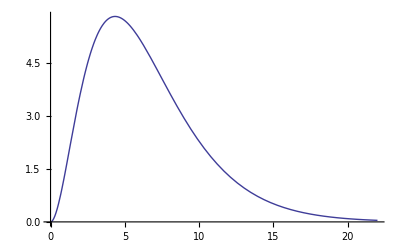

```mathematica
Plot[22.72727272727273 ⅇ^(-0.4605170185988092 m0) m0^2/10,{m0,0,22}]
```

```mathematica
15/√2*3600*24*365/149598000//N
```

```mathematica
2.2359242220650306*400
```

894.37

```mathematica
10
```

```mathematica
473040000/149598000//N
```

3.16207

```mathematica
10*10^((11.5-4.83)/5)
```

215.774

```mathematica
15/√2*215.8/894
```

2.5603

```mathematica
4861*(1+15/3*^5)//N
```

4861.24

```mathematica
Simplify@(b/.Simplify@Solve[b/(1-b^2)==g*z/c+c1,b][[1]]/.z->0)
```

-(c+√(c^2 (1+4 c1^2)))/(2 c c1)

```mathematica
bb[t_]:=b[t]/.DSolve[b'[t]/(1-b[t]^2)==g/c,b[t],t][[1]]/.C[1]->0
```

```mathematica
Integrate[1/√(1-bb[t]^2),{t,0,τ}]
```

```mathematica
Simplify@((c √(Sech[(g τ)/c]^2) Sinh[(2 g τ)/c])/(2 g))
```

(c √(Sech[(g τ)/c]^2) Sinh[(2 g τ)/c])/(2 g)

```mathematica
Simplify@√(Sech[(g τ)/c]^2)
```

√(Sech[(g τ)/c]^2)

```mathematica
√((6.4*^6+22-9.8*6.4*^6)/(6.4*^6-9.8*6.4*^6))-1
```

-1.95313×10^-7

```mathematica
l
```

```mathematica
0.999999804687481
```

```mathematica
1.999999804687481
```